### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                 (* K^-1 *);
Subscript[T, 0]          = 300                  (* K *);
Subscript[T, avg]       = 300                  (* K *);
Young   = 1.75 * 10^11  (* Па *);
σf          = 1.1 * 10^8      (* Па *);
ϵf          = 0.000628571 ;
l            = 10                     (* Длина стержня *);
Subscript[T, f]          =22                      (* Конечный момент времени *); 
Subscript[h, t]            = 0.05               (* Шаг времени *);
a            = 50                     (* Просто константа *);
n            =  5                      (* Число узлов сетки *);
Subscript[h, x]                                          (* Шаг сетки *);
];
```

### Определение функций распределения температуры в пространстве и времени

```mathematica
F[x_] := a Sin[(π x)/l];
Subscript[T, 1][x_, t_] := Subscript[T, avg] + F[x]t Sin[t];
Subscript[T, 2][ x_, t_ ] := Subscript[T, avg] + F[x] Cos[π t^2](t+1);
TT = Subscript[T, 1];
```

Тепловые деформации

```mathematica
Subscript[ϵ, t] [x_,tt_] := α(TT[x, tt] - Subscript[T, 0]);
```

```mathematica
Subscript[u, analytical] = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-Subscript[ϵ, t][x, t], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

Проверки для шага и количества точек (можем выставлять и то, и то)

```mathematica
If[NumberQ[n],
Subscript[h, x] = l/(n-1), 
If[NumberQ[Subscript[h, x]],n = IntegerPart[l/Subscript[h, x]]; Subscript[h, x] = l/n]
];
```

Создаем массив точек и значений функции f в них, далее решаем СЛАУ: Au = F(f(x_1), ..., f(x_n) ).

```mathematica
points = Table[i*Subscript[h, x], {i, 0, n-1}];
```

```mathematica
στ = Table[0,{i, 1, n}];                                     (* значения напряжений во временном слое τ *)
σfv = Table[σf,{i, 1, n}];                                (* значения переменных пределов прочности *)
ϵτ = Table[0,{i, 1, n}];                                            (* значения полных деформаций во временном слое τ *)
ϵe = Table[0,{i, 1, n}];                                     (* значения упругих деформаций во временном слое τ *)
ϵT = Table[0,{i, 1, n}];                                            (* значения температурных деформаций во врменном слое τ *) 
ϵcrk = Table[0,{i, 1, n}];                                        (* значения деформаций за счет трещин *) 
Tτ = Table[0,{i, 1, n}];                                            (* значения температуры во временном слое τ *) 
Subscript[balance, normal] [x_, k_]:= Young x;                             (* функция, подставляемая в условие равновесия при напряжениях, меньших предельных *) 
Subscript[balance, crack][x_, k_]:=  σfv⟦k⟧(A + B ⅇ^(-CC x/ϵf));   (* функция, подставляемая в условие равновесия при напряжениях, больших предельных *) 
balances =  Table[0,{i, 1, n}];                              (* функции равновесий на временном слое τ *) 
equations = Table[0,{i, 1, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
shifts = Table[0,{i, 1, n}];                                 (* сами перемещения *) 
cracking = Table[False,{i, 1, n}];                   (* нужно ли менять предел прочности*)
data = {};

For[τ = 0,τ≤Subscript[T, f],τ=τ+Subscript[h, t],
If[False, Break[]];
temp = {};
toprint = False;
For [i = 1, i≤ n+1, ++i,
Tτ⟦i⟧= TT[points⟦i⟧, τ];
ϵT⟦i⟧ = Subscript[ϵ, t][points⟦i⟧, τ];
memory =Young*( ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧); 
balances⟦i⟧ = If[memory < σfv⟦i⟧, 
cracking⟦i⟧ = False;Subscript[balance, normal],
toprint = True;cracking⟦i⟧ = True; Subscript[balance, crack]; Subscript[balance, normal]
];
];
If[toprint,Print@{"--------", τ, "--------"};];
iterations = 0;
While[Norm[(shifts - previous)/(Norm@previous + 10^-14)] ≥ 10^-7 || iterations == 0,
++iterations; 
equations⟦1⟧ = Subscript[y, 1] == 0;
For[i = 2, i < n, ++i,
Subscript[nonElastic, i+1/2] = (ϵT⟦i+1⟧+ ϵcrk⟦i+1⟧ + ϵT⟦i⟧+ ϵcrk⟦i⟧)/2; Subscript[nonElastic, i-1/2] = (ϵT⟦i⟧+ ϵcrk⟦i⟧ + ϵT⟦i-1⟧+ ϵcrk⟦i-1⟧)/2;
Subscript[v, i+1/2]= (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[v, i-1/2]=(shifts⟦i⟧ - shifts⟦i-1⟧)/Subscript[h, x]- Subscript[nonElastic, i-1/2];
Subscript[vnext, i+1/2] = (Subscript[y, i+1] - Subscript[y, i])/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[vnext, i-1/2]= (Subscript[y, i] - Subscript[y, i-1])/Subscript[h, x]- Subscript[nonElastic, i-1/2]; 
Subscript[dσ, i+1/2]= (balances⟦i⟧[Subscript[v, i+1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[Subscript[v, i+1/2], i])/(Subscript[h, x]/2); Subscript[dσ, i-1/2]=(balances⟦i⟧[ Subscript[v, i-1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[ Subscript[v, i-1/2], i])/(Subscript[h, x]/2);
equations⟦i⟧ = balances⟦i⟧[Subscript[v, i+1/2], i]+Subscript[dσ, i+1/2]*(Subscript[vnext, i+1/2] - Subscript[v, i+1/2])- balances⟦i⟧[Subscript[v, i-1/2], i]-Subscript[dσ, i-1/2]*(Subscript[vnext, i-1/2] - Subscript[v, i-1/2]) == 0;
];
equations⟦n⟧ = Subscript[y, n] == 0;
If[toprint, Print[MatrixForm@equations]];
previous = shifts;
shifts = #⟦2⟧&/@First@ Solve[equations] ;
If[toprint, Print[Solve[# == 0&/@equations]]];
];
For [i = 1, i< n, ++i,
ϵτ⟦i⟧ = (shifts⟦i + 1⟧ - shifts⟦i⟧)/Subscript[h, x];
If[cracking⟦i⟧,
σfv⟦i⟧=Subscript[balance, crack][ϵτ⟦i⟧ - ϵT⟦i⟧, i]; στ⟦i⟧ = σfv⟦i⟧; ϵcrk⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - στ⟦i⟧/Young; ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧,
ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧- ϵcrk⟦i⟧; στ⟦i⟧ = balances⟦i⟧[ϵe⟦i⟧, i]; 
];
AppendTo[temp, {τ, Tτ⟦i⟧, στ⟦i⟧, ϵτ⟦i⟧, ϵτ⟦i⟧-ϵT⟦i⟧, ϵcrk⟦i⟧}]
];
AppendTo[data, temp]
];
```

Part::partw: Part 6 of {0,5/2,5,15/2,10} does not exist.

Set::partw: Part 6 of {300,300,300,300,300} does not exist.

Part::partw: Part 6 of {0,5/2,5,15/2,10} does not exist.

Set::partw: Part 6 of {0,0,0,0,0} does not exist.

Part::partw: Part 6 of {0,0,0,0,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::partw: Part 6 of {balance_normal,balance_normal,balance_normal,balance_normal,balance_normal} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,0.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,0.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,-109329.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,109329.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{--------,3.55,--------}

(y_1==0
7.96839×10^6-1.75×10^11 (-0.000153468+2/5 (-y_1+y_2))+1.75×10^11 (0.000153468+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000153468+2/5 (-y_2+y_3))+1.75×10^11 (0.000153468+2/5 (-y_3+y_4))==0
-7.96839×10^6-1.75×10^11 (0.000153468+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153468+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(7.96839×10^6-1.75×10^11 (-0.000153468+2/5 Plus[«2»])+1.75×10^11 (0.000153468+2/5 Plus[«2»])==0)==0&&(0.-1.75×10^11 (0.000153468+2/5 Plus[«2»])+1.75×10^11 (0.000153468+2/5 Plus[«2»])==0)==0&&(-7.96839×10^6-1.75×10^11 (0.000153468+2/5 Plus[«2»])+1.75×10^11 (-0.000153468+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

Solve[{(y_1==0)==0,(7.96839×10^6-1.75×10^11 (-0.000153468+2/5 (-y_1+y_2))+1.75×10^11 (0.000153468+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000153468+2/5 (-y_2+y_3))+1.75×10^11 (0.000153468+2/5 (-y_3+y_4))==0)==0,(-7.96839×10^6-1.75×10^11 (0.000153468+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153468+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.49012×10^-8-1.75×10^11 (-0.000176234+2/5 (-y_1+y_2))+1.75×10^11 (0.000176234+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000176234+2/5 (-y_2+y_3))+1.75×10^11 (0.000176234+2/5 (-y_3+y_4))==0
1.49012×10^-8-1.75×10^11 (0.000176234+2/5 (-y_3+y_4))+1.75×10^11 (-0.000176234+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(-1.49012×10^-8-1.75×10^11 (-0.000176234+2/5 Plus[«2»])+1.75×10^11 (0.000176234+2/5 Plus[«2»])==0)==0&&(0.-1.75×10^11 (0.000176234+2/5 Plus[«2»])+1.75×10^11 (0.000176234+2/5 Plus[«2»])==0)==0&&(1.49012×10^-8-1.75×10^11 (0.000176234+2/5 Plus[«2»])+1.75×10^11 (-0.000176234+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

Solve[{(y_1==0)==0,(-1.49012×10^-8-1.75×10^11 (-0.000176234+2/5 (-y_1+y_2))+1.75×10^11 (0.000176234+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000176234+2/5 (-y_2+y_3))+1.75×10^11 (0.000176234+2/5 (-y_3+y_4))==0)==0,(1.49012×10^-8-1.75×10^11 (0.000176234+2/5 (-y_3+y_4))+1.75×10^11 (-0.000176234+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.6,--------}

(y_1==0
8.0149×10^6-1.75×10^11 (-0.000176234+2/5 (-y_1+y_2))+1.75×10^11 (0.000176234+2/5 (-y_2+y_3))==0
-6.01053×10^6-1.75×10^11 (0.000176234+2/5 (-y_2+y_3))+1.75×10^11 (0.000176234+2/5 (-y_3+y_4))==0
-8.0149×10^6-1.75×10^11 (0.000176234+2/5 (-y_3+y_4))+1.75×10^11 (-0.000176234+2/5 (-y_4+y_5))==0
y_5==0)

Solve::naqs: (y_1==0)==0&&(8.0149×10^6-1.75×10^11 (-0.000176234+2/5 Plus[«2»])+1.75×10^11 (0.000176234+2/5 Plus[«2»])==0)==0&&(-6.01053×10^6-1.75×10^11 (0.000176234+2/5 Plus[«2»])+1.75×10^11 (0.000176234+2/5 Plus[«2»])==0)==0&&(-8.0149×10^6-1.75×10^11 (0.000176234+2/5 Plus[«2»])+1.75×10^11 (-0.000176234+2/5 Plus[«2»])==0)==0&&(y_5==0)==0 is not a quantified system of equations and inequalities.

General::stop: Further output of Solve::naqs will be suppressed during this calculation.

Solve[{(y_1==0)==0,(8.0149×10^6-1.75×10^11 (-0.000176234+2/5 (-y_1+y_2))+1.75×10^11 (0.000176234+2/5 (-y_2+y_3))==0)==0,(-6.01053×10^6-1.75×10^11 (0.000176234+2/5 (-y_2+y_3))+1.75×10^11 (0.000176234+2/5 (-y_3+y_4))==0)==0,(-8.0149×10^6-1.75×10^11 (0.000176234+2/5 (-y_3+y_4))+1.75×10^11 (-0.000176234+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-0.000181961+2/5 (-y_1+y_2))+1.75×10^11 (0.000216307+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000216307+2/5 (-y_2+y_3))+1.75×10^11 (0.000181961+2/5 (-y_3+y_4))==0
2.98023×10^-8-1.75×10^11 (0.000181961+2/5 (-y_3+y_4))+1.75×10^11 (-0.000216307+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-0.000181961+2/5 (-y_1+y_2))+1.75×10^11 (0.000216307+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000216307+2/5 (-y_2+y_3))+1.75×10^11 (0.000181961+2/5 (-y_3+y_4))==0)==0,(2.98023×10^-8-1.75×10^11 (0.000181961+2/5 (-y_3+y_4))+1.75×10^11 (-0.000216307+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.65,--------}

(y_1==0
8.03677×10^6-1.75×10^11 (-0.000181961+2/5 (-y_1+y_2))+1.75×10^11 (0.000216307+2/5 (-y_2+y_3))==0
-1.52695×10^7-1.75×10^11 (0.000216307+2/5 (-y_2+y_3))+1.75×10^11 (0.000181961+2/5 (-y_3+y_4))==0
-8.03677×10^6-1.75×10^11 (0.000181961+2/5 (-y_3+y_4))+1.75×10^11 (-0.000216307+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(8.03677×10^6-1.75×10^11 (-0.000181961+2/5 (-y_1+y_2))+1.75×10^11 (0.000216307+2/5 (-y_2+y_3))==0)==0,(-1.52695×10^7-1.75×10^11 (0.000216307+2/5 (-y_2+y_3))+1.75×10^11 (0.000181961+2/5 (-y_3+y_4))==0)==0,(-8.03677×10^6-1.75×10^11 (0.000181961+2/5 (-y_3+y_4))+1.75×10^11 (-0.000216307+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.49012×10^-8-1.75×10^11 (-0.000161296+2/5 (-y_1+y_2))+1.75×10^11 (0.000282896+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000282896+2/5 (-y_2+y_3))+1.75×10^11 (0.000161296+2/5 (-y_3+y_4))==0
1.49012×10^-8-1.75×10^11 (0.000161296+2/5 (-y_3+y_4))+1.75×10^11 (-0.000282896+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.49012×10^-8-1.75×10^11 (-0.000161296+2/5 (-y_1+y_2))+1.75×10^11 (0.000282896+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000282896+2/5 (-y_2+y_3))+1.75×10^11 (0.000161296+2/5 (-y_3+y_4))==0)==0,(1.49012×10^-8-1.75×10^11 (0.000161296+2/5 (-y_3+y_4))+1.75×10^11 (-0.000282896+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.7,--------}

(y_1==0
-4.7792×10^6-1.75×10^11 (-0.000161296+2/5 (-y_1+y_2))+1.75×10^11 (0.000282896+2/5 (-y_2+y_3))==0
-2.11425×10^7-1.75×10^11 (0.000282896+2/5 (-y_2+y_3))+1.75×10^11 (0.000161296+2/5 (-y_3+y_4))==0
4.7792×10^6-1.75×10^11 (0.000161296+2/5 (-y_3+y_4))+1.75×10^11 (-0.000282896+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.7792×10^6-1.75×10^11 (-0.000161296+2/5 (-y_1+y_2))+1.75×10^11 (0.000282896+2/5 (-y_2+y_3))==0)==0,(-2.11425×10^7-1.75×10^11 (0.000282896+2/5 (-y_2+y_3))+1.75×10^11 (0.000161296+2/5 (-y_3+y_4))==0)==0,(4.7792×10^6-1.75×10^11 (0.000161296+2/5 (-y_3+y_4))+1.75×10^11 (-0.000282896+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.49012×10^-8-1.75×10^11 (-0.0000872344+2/5 (-y_1+y_2))+1.75×10^11 (0.000329649+2/5 (-y_2+y_3))==0
2.98023×10^-8-1.75×10^11 (0.000329649+2/5 (-y_2+y_3))+1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))==0
1.49012×10^-8-1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))+1.75×10^11 (-0.000329649+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.49012×10^-8-1.75×10^11 (-0.0000872344+2/5 (-y_1+y_2))+1.75×10^11 (0.000329649+2/5 (-y_2+y_3))==0)==0,(2.98023×10^-8-1.75×10^11 (0.000329649+2/5 (-y_2+y_3))+1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))==0)==0,(1.49012×10^-8-1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))+1.75×10^11 (-0.000329649+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.75,--------}

(y_1==0
-1.63345×10^7-1.75×10^11 (-0.0000872344+2/5 (-y_1+y_2))+1.75×10^11 (0.000329649+2/5 (-y_2+y_3))==0
-2.00227×10^7-1.75×10^11 (0.000329649+2/5 (-y_2+y_3))+1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))==0
1.63345×10^7-1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))+1.75×10^11 (-0.000329649+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.63345×10^7-1.75×10^11 (-0.0000872344+2/5 (-y_1+y_2))+1.75×10^11 (0.000329649+2/5 (-y_2+y_3))==0)==0,(-2.00227×10^7-1.75×10^11 (0.000329649+2/5 (-y_2+y_3))+1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))==0)==0,(1.63345×10^7-1.75×10^11 (0.0000872344+2/5 (-y_3+y_4))+1.75×10^11 (-0.000329649+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-7.45058×10^-9-1.75×10^11 (0.0000166434+2/5 (-y_1+y_2))+1.75×10^11 (0.000340186+2/5 (-y_2+y_3))==0
7.45058×10^-9-1.75×10^11 (0.000340186+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))==0
1.49012×10^-8-1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))+1.75×10^11 (-0.000340186+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-7.45058×10^-9-1.75×10^11 (0.0000166434+2/5 (-y_1+y_2))+1.75×10^11 (0.000340186+2/5 (-y_2+y_3))==0)==0,(7.45058×10^-9-1.75×10^11 (0.000340186+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))==0)==0,(1.49012×10^-8-1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))+1.75×10^11 (-0.000340186+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.8,--------}

(y_1==0
-2.19688×10^7-1.75×10^11 (0.0000166434+2/5 (-y_1+y_2))+1.75×10^11 (0.000340186+2/5 (-y_2+y_3))==0
-1.51926×10^7-1.75×10^11 (0.000340186+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))==0
2.19688×10^7-1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))+1.75×10^11 (-0.000340186+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.19688×10^7-1.75×10^11 (0.0000166434+2/5 (-y_1+y_2))+1.75×10^11 (0.000340186+2/5 (-y_2+y_3))==0)==0,(-1.51926×10^7-1.75×10^11 (0.000340186+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))==0)==0,(2.19688×10^7-1.75×10^11 (-0.0000166434+2/5 (-y_3+y_4))+1.75×10^11 (-0.000340186+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.000122819+2/5 (-y_1+y_2))+1.75×10^11 (0.000320826+2/5 (-y_2+y_3))==0
7.45058×10^-9-1.75×10^11 (0.000320826+2/5 (-y_2+y_3))+1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))==0
2.23517×10^-8-1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))+1.75×10^11 (-0.000320826+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.000122819+2/5 (-y_1+y_2))+1.75×10^11 (0.000320826+2/5 (-y_2+y_3))==0)==0,(7.45058×10^-9-1.75×10^11 (0.000320826+2/5 (-y_2+y_3))+1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))==0)==0,(2.23517×10^-8-1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))+1.75×10^11 (-0.000320826+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.85,--------}

(y_1==0
-2.10875×10^7-1.75×10^11 (0.000122819+2/5 (-y_1+y_2))+1.75×10^11 (0.000320826+2/5 (-y_2+y_3))==0
-1.02526×10^7-1.75×10^11 (0.000320826+2/5 (-y_2+y_3))+1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))==0
2.10875×10^7-1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))+1.75×10^11 (-0.000320826+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.10875×10^7-1.75×10^11 (0.000122819+2/5 (-y_1+y_2))+1.75×10^11 (0.000320826+2/5 (-y_2+y_3))==0)==0,(-1.02526×10^7-1.75×10^11 (0.000320826+2/5 (-y_2+y_3))+1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))==0)==0,(2.10875×10^7-1.75×10^11 (-0.000122819+2/5 (-y_3+y_4))+1.75×10^11 (-0.000320826+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.49012×10^-8-1.75×10^11 (0.000212362+2/5 (-y_1+y_2))+1.75×10^11 (0.000289869+2/5 (-y_2+y_3))==0
3.72529×10^-8-1.75×10^11 (0.000289869+2/5 (-y_2+y_3))+1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))==0
-2.98023×10^-8-1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))+1.75×10^11 (-0.000289869+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.49012×10^-8-1.75×10^11 (0.000212362+2/5 (-y_1+y_2))+1.75×10^11 (0.000289869+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-8-1.75×10^11 (0.000289869+2/5 (-y_2+y_3))+1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))==0)==0,(-2.98023×10^-8-1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))+1.75×10^11 (-0.000289869+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.9,--------}

(y_1==0
-1.61138×10^7-1.75×10^11 (0.000212362+2/5 (-y_1+y_2))+1.75×10^11 (0.000289869+2/5 (-y_2+y_3))==0
-7.22129×10^6-1.75×10^11 (0.000289869+2/5 (-y_2+y_3))+1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))==0
1.61138×10^7-1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))+1.75×10^11 (-0.000289869+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.61138×10^7-1.75×10^11 (0.000212362+2/5 (-y_1+y_2))+1.75×10^11 (0.000289869+2/5 (-y_2+y_3))==0)==0,(-7.22129×10^6-1.75×10^11 (0.000289869+2/5 (-y_2+y_3))+1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))==0)==0,(1.61138×10^7-1.75×10^11 (-0.000212362+2/5 (-y_3+y_4))+1.75×10^11 (-0.000289869+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-7.45058×10^-9-1.75×10^11 (0.000279034+2/5 (-y_1+y_2))+1.75×10^11 (0.000264461+2/5 (-y_2+y_3))==0
3.72529×10^-8-1.75×10^11 (0.000264461+2/5 (-y_2+y_3))+1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))==0
-7.45058×10^-9-1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))+1.75×10^11 (-0.000264461+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-7.45058×10^-9-1.75×10^11 (0.000279034+2/5 (-y_1+y_2))+1.75×10^11 (0.000264461+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-8-1.75×10^11 (0.000264461+2/5 (-y_2+y_3))+1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))==0)==0,(-7.45058×10^-9-1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))+1.75×10^11 (-0.000264461+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,3.95,--------}

(y_1==0
-1.05855×10^7-1.75×10^11 (0.000279034+2/5 (-y_1+y_2))+1.75×10^11 (0.000264461+2/5 (-y_2+y_3))==0
1.00131×10^6-1.75×10^11 (0.000264461+2/5 (-y_2+y_3))+1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))==0
1.05855×10^7-1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))+1.75×10^11 (-0.000264461+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.05855×10^7-1.75×10^11 (0.000279034+2/5 (-y_1+y_2))+1.75×10^11 (0.000264461+2/5 (-y_2+y_3))==0)==0,(1.00131×10^6-1.75×10^11 (0.000264461+2/5 (-y_2+y_3))+1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))==0)==0,(1.05855×10^7-1.75×10^11 (-0.000279034+2/5 (-y_3+y_4))+1.75×10^11 (-0.000264461+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
7.45058×10^-9-1.75×10^11 (0.000306417+2/5 (-y_1+y_2))+1.75×10^11 (0.000231356+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.000231356+2/5 (-y_2+y_3))+1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))==0
1.86265×10^-8-1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))+1.75×10^11 (-0.000231356+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(7.45058×10^-9-1.75×10^11 (0.000306417+2/5 (-y_1+y_2))+1.75×10^11 (0.000231356+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.000231356+2/5 (-y_2+y_3))+1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))==0)==0,(1.86265×10^-8-1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))+1.75×10^11 (-0.000231356+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.,--------}

(y_1==0
-4.74534×10^6-1.75×10^11 (0.000306417+2/5 (-y_1+y_2))+1.75×10^11 (0.000231356+2/5 (-y_2+y_3))==0
9.9142×10^6-1.75×10^11 (0.000231356+2/5 (-y_2+y_3))+1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))==0
4.74534×10^6-1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))+1.75×10^11 (-0.000231356+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.74534×10^6-1.75×10^11 (0.000306417+2/5 (-y_1+y_2))+1.75×10^11 (0.000231356+2/5 (-y_2+y_3))==0)==0,(9.9142×10^6-1.75×10^11 (0.000231356+2/5 (-y_2+y_3))+1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))==0)==0,(4.74534×10^6-1.75×10^11 (-0.000306417+2/5 (-y_3+y_4))+1.75×10^11 (-0.000231356+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
1.11759×10^-8-1.75×10^11 (0.000291649+2/5 (-y_1+y_2))+1.75×10^11 (0.000189472+2/5 (-y_2+y_3))==0
-1.86265×10^-8-1.75×10^11 (0.000189472+2/5 (-y_2+y_3))+1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))==0
4.47035×10^-8-1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))+1.75×10^11 (-0.000189472+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.11759×10^-8-1.75×10^11 (0.000291649+2/5 (-y_1+y_2))+1.75×10^11 (0.000189472+2/5 (-y_2+y_3))==0)==0,(-1.86265×10^-8-1.75×10^11 (0.000189472+2/5 (-y_2+y_3))+1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))==0)==0,(4.47035×10^-8-1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))+1.75×10^11 (-0.000189472+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.05,--------}

(y_1==0
192256.-1.75×10^11 (0.000291649+2/5 (-y_1+y_2))+1.75×10^11 (0.000189472+2/5 (-y_2+y_3))==0
1.47949×10^7-1.75×10^11 (0.000189472+2/5 (-y_2+y_3))+1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))==0
-192256.-1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))+1.75×10^11 (-0.000189472+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(192256.-1.75×10^11 (0.000291649+2/5 (-y_1+y_2))+1.75×10^11 (0.000189472+2/5 (-y_2+y_3))==0)==0,(1.47949×10^7-1.75×10^11 (0.000189472+2/5 (-y_2+y_3))+1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))==0)==0,(-192256.-1.75×10^11 (-0.000291649+2/5 (-y_3+y_4))+1.75×10^11 (-0.000189472+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-9.31323×10^-9-1.75×10^11 (0.000248829+2/5 (-y_1+y_2))+1.75×10^11 (0.00014775+2/5 (-y_2+y_3))==0
3.72529×10^-8-1.75×10^11 (0.00014775+2/5 (-y_2+y_3))+1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))==0
-3.35276×10^-8-1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))+1.75×10^11 (-0.00014775+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-9.31323×10^-9-1.75×10^11 (0.000248829+2/5 (-y_1+y_2))+1.75×10^11 (0.00014775+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-8-1.75×10^11 (0.00014775+2/5 (-y_2+y_3))+1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))==0)==0,(-3.35276×10^-8-1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))+1.75×10^11 (-0.00014775+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.1,--------}

(y_1==0
3.18031×10^6-1.75×10^11 (0.000248829+2/5 (-y_1+y_2))+1.75×10^11 (0.00014775+2/5 (-y_2+y_3))==0
1.60724×10^7-1.75×10^11 (0.00014775+2/5 (-y_2+y_3))+1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))==0
-3.18031×10^6-1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))+1.75×10^11 (-0.00014775+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(3.18031×10^6-1.75×10^11 (0.000248829+2/5 (-y_1+y_2))+1.75×10^11 (0.00014775+2/5 (-y_2+y_3))==0)==0,(1.60724×10^7-1.75×10^11 (0.00014775+2/5 (-y_2+y_3))+1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))==0)==0,(-3.18031×10^6-1.75×10^11 (-0.000248829+2/5 (-y_3+y_4))+1.75×10^11 (-0.00014775+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
9.31323×10^-9-1.75×10^11 (0.000193821+2/5 (-y_1+y_2))+1.75×10^11 (0.000110916+2/5 (-y_2+y_3))==0
2.79397×10^-8-1.75×10^11 (0.000110916+2/5 (-y_2+y_3))+1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))==0
-9.31323×10^-9-1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))+1.75×10^11 (-0.000110916+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(9.31323×10^-9-1.75×10^11 (0.000193821+2/5 (-y_1+y_2))+1.75×10^11 (0.000110916+2/5 (-y_2+y_3))==0)==0,(2.79397×10^-8-1.75×10^11 (0.000110916+2/5 (-y_2+y_3))+1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))==0)==0,(-9.31323×10^-9-1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))+1.75×10^11 (-0.000110916+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.15,--------}

(y_1==0
4.44191×10^6-1.75×10^11 (0.000193821+2/5 (-y_1+y_2))+1.75×10^11 (0.000110916+2/5 (-y_2+y_3))==0
1.472×10^7-1.75×10^11 (0.000110916+2/5 (-y_2+y_3))+1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))==0
-4.44191×10^6-1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))+1.75×10^11 (-0.000110916+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(4.44191×10^6-1.75×10^11 (0.000193821+2/5 (-y_1+y_2))+1.75×10^11 (0.000110916+2/5 (-y_2+y_3))==0)==0,(1.472×10^7-1.75×10^11 (0.000110916+2/5 (-y_2+y_3))+1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))==0)==0,(-4.44191×10^6-1.75×10^11 (-0.000193821+2/5 (-y_3+y_4))+1.75×10^11 (-0.000110916+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-5.58794×10^-9-1.75×10^11 (0.000139073+2/5 (-y_1+y_2))+1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))==0
5.58794×10^-9-1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))+1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000815496+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-5.58794×10^-9-1.75×10^11 (0.000139073+2/5 (-y_1+y_2))+1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))==0)==0,(5.58794×10^-9-1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))+1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000815496+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.2,--------}

(y_1==0
4.47615×10^6-1.75×10^11 (0.000139073+2/5 (-y_1+y_2))+1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))==0
1.18524×10^7-1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))+1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))==0
-4.47615×10^6-1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000815496+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(4.47615×10^6-1.75×10^11 (0.000139073+2/5 (-y_1+y_2))+1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))==0)==0,(1.18524×10^7-1.75×10^11 (0.0000815496+2/5 (-y_2+y_3))+1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))==0)==0,(-4.47615×10^6-1.75×10^11 (-0.000139073+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000815496+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000924196+2/5 (-y_1+y_2))+1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))==0
9.31323×10^-9-1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000604748+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000924196+2/5 (-y_1+y_2))+1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-9-1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000604748+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.25,--------}

(y_1==0
3.77235×10^6-1.75×10^11 (0.0000924196+2/5 (-y_1+y_2))+1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))==0
8.54556×10^6-1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))==0
-3.77235×10^6-1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000604748+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(3.77235×10^6-1.75×10^11 (0.0000924196+2/5 (-y_1+y_2))+1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))==0)==0,(8.54556×10^6-1.75×10^11 (0.0000604748+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))==0)==0,(-3.77235×10^6-1.75×10^11 (-0.0000924196+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000604748+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000572256+2/5 (-y_1+y_2))+1.75×10^11 (0.000046837+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.000046837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))+1.75×10^11 (-0.000046837+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000572256+2/5 (-y_1+y_2))+1.75×10^11 (0.000046837+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.000046837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))+1.75×10^11 (-0.000046837+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.3,--------}

(y_1==0
2.75527×10^6-1.75×10^11 (0.0000572256+2/5 (-y_1+y_2))+1.75×10^11 (0.000046837+2/5 (-y_2+y_3))==0
5.59879×10^6-1.75×10^11 (0.000046837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))==0
-2.75527×10^6-1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))+1.75×10^11 (-0.000046837+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(2.75527×10^6-1.75×10^11 (0.0000572256+2/5 (-y_1+y_2))+1.75×10^11 (0.000046837+2/5 (-y_2+y_3))==0)==0,(5.59879×10^6-1.75×10^11 (0.000046837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))==0)==0,(-2.75527×10^6-1.75×10^11 (-0.0000572256+2/5 (-y_3+y_4))+1.75×10^11 (-0.000046837+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000333569+2/5 (-y_1+y_2))+1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))==0
-9.31323×10^-10-1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000387127+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000333569+2/5 (-y_1+y_2))+1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))==0)==0,(-9.31323×10^-10-1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000387127+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.35,--------}

(y_1==0
1.7434×10^6-1.75×10^11 (0.0000333569+2/5 (-y_1+y_2))+1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))==0
3.39854×10^6-1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))==0
-1.7434×10^6-1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000387127+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.7434×10^6-1.75×10^11 (0.0000333569+2/5 (-y_1+y_2))+1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))==0)==0,(3.39854×10^6-1.75×10^11 (0.0000387127+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))==0)==0,(-1.7434×10^6-1.75×10^11 (-0.0000333569+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000387127+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000186656+2/5 (-y_1+y_2))+1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))==0
1.86265×10^-9-1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))==0
2.79397×10^-9-1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000339837+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000186656+2/5 (-y_1+y_2))+1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))==0)==0,(1.86265×10^-9-1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))==0)==0,(2.79397×10^-9-1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000339837+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.4,--------}

(y_1==0
917577.-1.75×10^11 (0.0000186656+2/5 (-y_1+y_2))+1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))==0
1.9745×10^6-1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))==0
-917577.-1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000339837+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(917577.-1.75×10^11 (0.0000186656+2/5 (-y_1+y_2))+1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))==0)==0,(1.9745×10^6-1.75×10^11 (0.0000339837+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))==0)==0,(-917577.-1.75×10^11 (-0.0000186656+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000339837+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-9.31323×10^-10-1.75×10^11 (0.0000104025+2/5 (-y_1+y_2))+1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))==0
9.31323×10^-10-1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))==0
9.31323×10^-10-1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000309639+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-9.31323×10^-10-1.75×10^11 (0.0000104025+2/5 (-y_1+y_2))+1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))==0)==0,(9.31323×10^-10-1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-10-1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000309639+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.45,--------}

(y_1==0
332157.-1.75×10^11 (0.0000104025+2/5 (-y_1+y_2))+1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))==0
1.16145×10^6-1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))==0
-332157.-1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000309639+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(332157.-1.75×10^11 (0.0000104025+2/5 (-y_1+y_2))+1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))==0)==0,(1.16145×10^6-1.75×10^11 (0.0000309639+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))==0)==0,(-332157.-1.75×10^11 (-0.0000104025+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000309639+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-9.31323×10^-10-1.75×10^11 (6.13508×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))==0
9.31323×10^-10-1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))+1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000285945+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-9.31323×10^-10-1.75×10^11 (6.13508×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))==0)==0,(9.31323×10^-10-1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))+1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000285945+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.5,--------}

(y_1==0
-39901.6-1.75×10^11 (6.13508×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))==0
748977.-1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))+1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))==0
39901.6-1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000285945+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-39901.6-1.75×10^11 (6.13508×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))==0)==0,(748977.-1.75×10^11 (0.0000285945+2/5 (-y_2+y_3))+1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))==0)==0,(39901.6-1.75×10^11 (-6.13508×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000285945+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (4.10915×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))+1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))==0
2.79397×10^-9-1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000263406+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (4.10915×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))+1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))==0)==0,(2.79397×10^-9-1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000263406+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.55,--------}

(y_1==0
-257684.-1.75×10^11 (4.10915×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))==0
564167.-1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))+1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))==0
257684.-1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000263406+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-257684.-1.75×10^11 (4.10915×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))==0)==0,(564167.-1.75×10^11 (0.0000263406+2/5 (-y_2+y_3))+1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))==0)==0,(257684.-1.75×10^11 (-4.10915×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000263406+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (3.23349×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))==0
9.31323×10^-10-1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))+1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000239925+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (3.23349×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))==0)==0,(9.31323×10^-10-1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))+1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000239925+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.6,--------}

(y_1==0
-379039.-1.75×10^11 (3.23349×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))==0
494038.-1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))+1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))==0
379039.-1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000239925+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-379039.-1.75×10^11 (3.23349×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))==0)==0,(494038.-1.75×10^11 (0.0000239925+2/5 (-y_2+y_3))+1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))==0)==0,(379039.-1.75×10^11 (-3.23349×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000239925+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (2.90492×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))==0
-4.65661×10^-10-1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))+1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))==0
-9.31323×10^-10-1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000214979+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (2.90492×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))==0)==0,(-4.65661×10^-10-1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))+1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))==0)==0,(-9.31323×10^-10-1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000214979+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.65,--------}

(y_1==0
-446575.-1.75×10^11 (2.90492×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))==0
475925.-1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))+1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))==0
446575.-1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000214979+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-446575.-1.75×10^11 (2.90492×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))==0)==0,(475925.-1.75×10^11 (0.0000214979+2/5 (-y_2+y_3))+1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))==0)==0,(446575.-1.75×10^11 (-2.90492×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000214979+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-9.31323×10^-10-1.75×10^11 (2.82106×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))==0
1.39698×10^-9-1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))+1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))==0
-4.65661×10^-10-1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000188622+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-9.31323×10^-10-1.75×10^11 (2.82106×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))==0)==0,(1.39698×10^-9-1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))+1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))==0)==0,(-4.65661×10^-10-1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000188622+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.7,--------}

(y_1==0
-486528.-1.75×10^11 (2.82106×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))==0
479371.-1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))+1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))==0
486528.-1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000188622+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-486528.-1.75×10^11 (2.82106×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))==0)==0,(479371.-1.75×10^11 (0.0000188622+2/5 (-y_2+y_3))+1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))==0)==0,(486528.-1.75×10^11 (-2.82106×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000188622+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-4.65661×10^-10-1.75×10^11 (2.84151×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))==0
4.65661×10^-10-1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))+1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))==0
4.65661×10^-10-1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000161025+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.65661×10^-10-1.75×10^11 (2.84151×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))==0)==0,(4.65661×10^-10-1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))+1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))==0)==0,(4.65661×10^-10-1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000161025+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.75,--------}

(y_1==0
-512997.-1.75×10^11 (2.84151×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))==0
491071.-1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))+1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))==0
512997.-1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000161025+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-512997.-1.75×10^11 (2.84151×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))==0)==0,(491071.-1.75×10^11 (0.0000161025+2/5 (-y_2+y_3))+1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))==0)==0,(512997.-1.75×10^11 (-2.84151×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000161025+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (2.90416×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))+1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))==0
9.31323×10^-10-1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000132338+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (2.90416×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))+1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-10-1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000132338+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.8,--------}

(y_1==0
-532759.-1.75×10^11 (2.90416×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))==0
505591.-1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))+1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))==0
532759.-1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000132338+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-532759.-1.75×10^11 (2.90416×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))==0)==0,(505591.-1.75×10^11 (0.0000132338+2/5 (-y_2+y_3))+1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))==0)==0,(532759.-1.75×10^11 (-2.90416×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000132338+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (2.98178×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000010267+2/5 (-y_2+y_3))==0
-2.32831×10^-10-1.75×10^11 (0.000010267+2/5 (-y_2+y_3))+1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))==0
9.31323×10^-10-1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000010267+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (2.98178×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000010267+2/5 (-y_2+y_3))==0)==0,(-2.32831×10^-10-1.75×10^11 (0.000010267+2/5 (-y_2+y_3))+1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-10-1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000010267+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.85,--------}

(y_1==0
-548802.-1.75×10^11 (2.98178×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000010267+2/5 (-y_2+y_3))==0
520704.-1.75×10^11 (0.000010267+2/5 (-y_2+y_3))+1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))==0
548802.-1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000010267+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-548802.-1.75×10^11 (2.98178×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000010267+2/5 (-y_2+y_3))==0)==0,(520704.-1.75×10^11 (0.000010267+2/5 (-y_2+y_3))+1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))==0)==0,(548802.-1.75×10^11 (-2.98178×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000010267+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-4.65661×10^-10-1.75×10^11 (3.06206×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))==0
-4.65661×10^-10-1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-7.21131×10^-6+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.65661×10^-10-1.75×10^11 (3.06206×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))==0)==0,(-4.65661×10^-10-1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-7.21131×10^-6+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,4.9,--------}

(y_1==0
-562364.-1.75×10^11 (3.06206×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))==0
535399.-1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))==0
562364.-1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-7.21131×10^-6+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-562364.-1.75×10^11 (3.06206×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))==0)==0,(535399.-1.75×10^11 (7.21131×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))==0)==0,(562364.-1.75×10^11 (-3.06206×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-7.21131×10^-6+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-2.91038×10^-10-1.75×10^11 (3.1391×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (4.07485×10^-6+2/5 (-y_2+y_3))==0
2.91038×10^-10-1.75×10^11 (4.07485×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.1391×10^-6+2/5 (-y_3+y_4))==0
-1.16415×10^-10-1.75×10^11 (-3.1391×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-4.07485×10^-6+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.91038×10^-10-1.75×10^11 (3.1391×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (4.07485×10^-6+2/5 (-y_2+y_3))==0)==0,(2.91038×10^-10-1.75×10^11 (4.07485×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-3.1391×10^-6+2/5 (-y_3+y_4))==0)==0,(-1.16415×10^-10-1.75×10^11 (-3.1391×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-4.07485×10^-6+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,9.95,--------}

(y_1==0
2.00977×10^7-1.75×10^11 (0.0000383743+2/5 (-y_1+y_2))+1.75×10^11 (-0.0000342984+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (-0.0000342984+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000383743+2/5 (-y_3+y_4))==0
-2.00977×10^7-1.75×10^11 (-0.0000383743+2/5 (-y_3+y_4))+1.75×10^11 (0.0000342984+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(2.00977×10^7-1.75×10^11 (0.0000383743+2/5 (-y_1+y_2))+1.75×10^11 (-0.0000342984+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (-0.0000342984+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000383743+2/5 (-y_3+y_4))==0)==0,(-2.00977×10^7-1.75×10^11 (-0.0000383743+2/5 (-y_3+y_4))+1.75×10^11 (0.0000342984+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
1.86265×10^-9-1.75×10^11 (-0.0000190477+2/5 (-y_1+y_2))+1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))+1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))==0
1.86265×10^-9-1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000231236+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.86265×10^-9-1.75×10^11 (-0.0000190477+2/5 (-y_1+y_2))+1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))+1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))==0)==0,(1.86265×10^-9-1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000231236+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.,--------}

(y_1==0
1.4028×10^7-1.75×10^11 (-0.0000190477+2/5 (-y_1+y_2))+1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))==0
-3.33342×10^6-1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))+1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))==0
-1.4028×10^7-1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000231236+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.4028×10^7-1.75×10^11 (-0.0000190477+2/5 (-y_1+y_2))+1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))==0)==0,(-3.33342×10^6-1.75×10^11 (0.0000231236+2/5 (-y_2+y_3))+1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))==0)==0,(-1.4028×10^7-1.75×10^11 (0.0000190477+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000231236+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-0.0000496037+2/5 (-y_1+y_2))+1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))+1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000727277+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-0.0000496037+2/5 (-y_1+y_2))+1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))+1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000727277+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.05,--------}

(y_1==0
2.26222×10^6-1.75×10^11 (-0.0000496037+2/5 (-y_1+y_2))+1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))==0
-8.68067×10^6-1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))+1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))==0
-2.26222×10^6-1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000727277+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(2.26222×10^6-1.75×10^11 (-0.0000496037+2/5 (-y_1+y_2))+1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))==0)==0,(-8.68067×10^6-1.75×10^11 (0.0000727277+2/5 (-y_2+y_3))+1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))==0)==0,(-2.26222×10^6-1.75×10^11 (0.0000496037+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000727277+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-0.0000312652+2/5 (-y_1+y_2))+1.75×10^11 (0.000103993+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.000103993+2/5 (-y_2+y_3))+1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))==0
1.49012×10^-8-1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))+1.75×10^11 (-0.000103993+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-0.0000312652+2/5 (-y_1+y_2))+1.75×10^11 (0.000103993+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.000103993+2/5 (-y_2+y_3))+1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))==0)==0,(1.49012×10^-8-1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))+1.75×10^11 (-0.000103993+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.1,--------}

(y_1==0
-2.07053×10^6-1.75×10^11 (-0.0000312652+2/5 (-y_1+y_2))+1.75×10^11 (0.000103993+2/5 (-y_2+y_3))==0
-5.47143×10^6-1.75×10^11 (0.000103993+2/5 (-y_2+y_3))+1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))==0
2.07053×10^6-1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))+1.75×10^11 (-0.000103993+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.07053×10^6-1.75×10^11 (-0.0000312652+2/5 (-y_1+y_2))+1.75×10^11 (0.000103993+2/5 (-y_2+y_3))==0)==0,(-5.47143×10^6-1.75×10^11 (0.000103993+2/5 (-y_2+y_3))+1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))==0)==0,(2.07053×10^6-1.75×10^11 (0.0000312652+2/5 (-y_3+y_4))+1.75×10^11 (-0.000103993+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-3.72529×10^-9-1.75×10^11 (-9.71679×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.00011371+2/5 (-y_2+y_3))==0
7.45058×10^-9-1.75×10^11 (0.00011371+2/5 (-y_2+y_3))+1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))==0
-3.72529×10^-9-1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.00011371+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.72529×10^-9-1.75×10^11 (-9.71679×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.00011371+2/5 (-y_2+y_3))==0)==0,(7.45058×10^-9-1.75×10^11 (0.00011371+2/5 (-y_2+y_3))+1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))==0)==0,(-3.72529×10^-9-1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.00011371+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.15,--------}

(y_1==0
-2.40517×10^6-1.75×10^11 (-9.71679×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.00011371+2/5 (-y_2+y_3))==0
-1.70044×10^6-1.75×10^11 (0.00011371+2/5 (-y_2+y_3))+1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))==0
2.40517×10^6-1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.00011371+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.40517×10^6-1.75×10^11 (-9.71679×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.00011371+2/5 (-y_2+y_3))==0)==0,(-1.70044×10^6-1.75×10^11 (0.00011371+2/5 (-y_2+y_3))+1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))==0)==0,(2.40517×10^6-1.75×10^11 (9.71679×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.00011371+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
7.45058×10^-9-1.75×10^11 (2.01354×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000111696+2/5 (-y_2+y_3))==0
-7.45058×10^-9-1.75×10^11 (0.000111696+2/5 (-y_2+y_3))+1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))==0
7.45058×10^-9-1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000111696+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(7.45058×10^-9-1.75×10^11 (2.01354×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000111696+2/5 (-y_2+y_3))==0)==0,(-7.45058×10^-9-1.75×10^11 (0.000111696+2/5 (-y_2+y_3))+1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))==0)==0,(7.45058×10^-9-1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000111696+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.2,--------}

(y_1==0
-1.59899×10^6-1.75×10^11 (2.01354×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000111696+2/5 (-y_2+y_3))==0
352368.-1.75×10^11 (0.000111696+2/5 (-y_2+y_3))+1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))==0
1.59899×10^6-1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000111696+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.59899×10^6-1.75×10^11 (2.01354×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000111696+2/5 (-y_2+y_3))==0)==0,(352368.-1.75×10^11 (0.000111696+2/5 (-y_2+y_3))+1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))==0)==0,(1.59899×10^6-1.75×10^11 (-2.01354×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000111696+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (5.5753×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000106121+2/5 (-y_2+y_3))==0
-7.45058×10^-9-1.75×10^11 (0.000106121+2/5 (-y_2+y_3))+1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))==0
1.11759×10^-8-1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000106121+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (5.5753×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000106121+2/5 (-y_2+y_3))==0)==0,(-7.45058×10^-9-1.75×10^11 (0.000106121+2/5 (-y_2+y_3))+1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))==0)==0,(1.11759×10^-8-1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000106121+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.25,--------}

(y_1==0
-936109.-1.75×10^11 (5.5753×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000106121+2/5 (-y_2+y_3))==0
975677.-1.75×10^11 (0.000106121+2/5 (-y_2+y_3))+1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))==0
936109.-1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000106121+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-936109.-1.75×10^11 (5.5753×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000106121+2/5 (-y_2+y_3))==0)==0,(975677.-1.75×10^11 (0.000106121+2/5 (-y_2+y_3))+1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))==0)==0,(936109.-1.75×10^11 (-5.5753×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000106121+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (5.46225×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000100659+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000100659+2/5 (-y_2+y_3))+1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))==0
1.11759×10^-8-1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000100659+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (5.46225×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000100659+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000100659+2/5 (-y_2+y_3))+1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))==0)==0,(1.11759×10^-8-1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000100659+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.3,--------}

(y_1==0
-665265.-1.75×10^11 (5.46225×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000100659+2/5 (-y_2+y_3))==0
955893.-1.75×10^11 (0.000100659+2/5 (-y_2+y_3))+1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))==0
665265.-1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000100659+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-665265.-1.75×10^11 (5.46225×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000100659+2/5 (-y_2+y_3))==0)==0,(955893.-1.75×10^11 (0.000100659+2/5 (-y_2+y_3))+1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))==0)==0,(665265.-1.75×10^11 (-5.46225×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000100659+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
7.45058×10^-9-1.75×10^11 (4.63188×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000096027+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000096027+2/5 (-y_2+y_3))+1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000096027+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(7.45058×10^-9-1.75×10^11 (4.63188×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000096027+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000096027+2/5 (-y_2+y_3))+1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000096027+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.35,--------}

(y_1==0
-651887.-1.75×10^11 (4.63188×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000096027+2/5 (-y_2+y_3))==0
810579.-1.75×10^11 (0.000096027+2/5 (-y_2+y_3))+1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))==0
651887.-1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000096027+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-651887.-1.75×10^11 (4.63188×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000096027+2/5 (-y_2+y_3))==0)==0,(810579.-1.75×10^11 (0.000096027+2/5 (-y_2+y_3))+1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))==0)==0,(651887.-1.75×10^11 (-4.63188×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000096027+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (4.17847×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))+1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000918485+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (4.17847×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))+1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000918485+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.4,--------}

(y_1==0
-732796.-1.75×10^11 (4.17847×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))==0
731233.-1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))+1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))==0
732796.-1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000918485+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-732796.-1.75×10^11 (4.17847×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))==0)==0,(731233.-1.75×10^11 (0.0000918485+2/5 (-y_2+y_3))+1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))==0)==0,(732796.-1.75×10^11 (-4.17847×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000918485+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (4.18294×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))+1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000876656+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (4.18294×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))+1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000876656+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.45,--------}

(y_1==0
-819183.-1.75×10^11 (4.18294×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))==0
732014.-1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))+1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))==0
819183.-1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000876656+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-819183.-1.75×10^11 (4.18294×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))==0)==0,(732014.-1.75×10^11 (0.0000876656+2/5 (-y_2+y_3))+1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))==0)==0,(819183.-1.75×10^11 (-4.18294×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000876656+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-3.72529×10^-9-1.75×10^11 (4.43199×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))+1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000832336+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.72529×10^-9-1.75×10^11 (4.43199×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))+1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000832336+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.5,--------}

(y_1==0
-885168.-1.75×10^11 (4.43199×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))==0
775599.-1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))+1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))==0
885168.-1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000832336+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-885168.-1.75×10^11 (4.43199×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))==0)==0,(775599.-1.75×10^11 (0.0000832336+2/5 (-y_2+y_3))+1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))==0)==0,(885168.-1.75×10^11 (-4.43199×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000832336+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.86265×10^-9-1.75×10^11 (4.74505×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))==0
5.58794×10^-9-1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))+1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000784885+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.86265×10^-9-1.75×10^11 (4.74505×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))==0)==0,(5.58794×10^-9-1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))+1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000784885+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.55,--------}

(y_1==0
-933477.-1.75×10^11 (4.74505×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))==0
830383.-1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))+1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))==0
933477.-1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000784885+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-933477.-1.75×10^11 (4.74505×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))==0)==0,(830383.-1.75×10^11 (0.0000784885+2/5 (-y_2+y_3))+1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))==0)==0,(933477.-1.75×10^11 (-4.74505×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000784885+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (5.0396×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))==0
7.45058×10^-9-1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))+1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))==0
-5.58794×10^-9-1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000734489+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (5.0396×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))==0)==0,(7.45058×10^-9-1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))+1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))==0)==0,(-5.58794×10^-9-1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000734489+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.6,--------}

(y_1==0
-972562.-1.75×10^11 (5.0396×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))==0
881930.-1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))+1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))==0
972562.-1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000734489+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-972562.-1.75×10^11 (5.0396×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))==0)==0,(881930.-1.75×10^11 (0.0000734489+2/5 (-y_2+y_3))+1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))==0)==0,(972562.-1.75×10^11 (-5.0396×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000734489+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
1.86265×10^-9-1.75×10^11 (5.29855×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))+1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))==0
7.45058×10^-9-1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000681504+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.86265×10^-9-1.75×10^11 (5.29855×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))+1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))==0)==0,(7.45058×10^-9-1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000681504+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.65,--------}

(y_1==0
-1.00802×10^6-1.75×10^11 (5.29855×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))==0
927246.-1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))+1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))==0
1.00802×10^6-1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000681504+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.00802×10^6-1.75×10^11 (5.29855×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))==0)==0,(927246.-1.75×10^11 (0.0000681504+2/5 (-y_2+y_3))+1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))==0)==0,(1.00802×10^6-1.75×10^11 (-5.29855×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000681504+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (5.52933×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))==0
1.86265×10^-9-1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))+1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))==0
9.31323×10^-9-1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000626211+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (5.52933×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))==0)==0,(1.86265×10^-9-1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))+1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-9-1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000626211+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.7,--------}

(y_1==0
-1.04188×10^6-1.75×10^11 (5.52933×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))==0
967633.-1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))+1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))==0
1.04188×10^6-1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000626211+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.04188×10^6-1.75×10^11 (5.52933×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))==0)==0,(967633.-1.75×10^11 (0.0000626211+2/5 (-y_2+y_3))+1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))==0)==0,(1.04188×10^6-1.75×10^11 (-5.52933×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000626211+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
1.86265×10^-9-1.75×10^11 (5.74146×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))+1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))==0
9.31323×10^-9-1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000568796+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(1.86265×10^-9-1.75×10^11 (5.74146×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))+1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))==0)==0,(9.31323×10^-9-1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000568796+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.75,--------}

(y_1==0
-1.0742×10^6-1.75×10^11 (5.74146×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))==0
1.00476×10^6-1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))+1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))==0
1.0742×10^6-1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000568796+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.0742×10^6-1.75×10^11 (5.74146×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))==0)==0,(1.00476×10^6-1.75×10^11 (0.0000568796+2/5 (-y_2+y_3))+1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))==0)==0,(1.0742×10^6-1.75×10^11 (-5.74146×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000568796+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-3.72529×10^-9-1.75×10^11 (5.93986×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))+1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000509397+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.72529×10^-9-1.75×10^11 (5.93986×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))+1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000509397+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.8,--------}

(y_1==0
-1.10447×10^6-1.75×10^11 (5.93986×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))==0
1.03948×10^6-1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))+1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))==0
1.10447×10^6-1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000509397+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.10447×10^6-1.75×10^11 (5.93986×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))==0)==0,(1.03948×10^6-1.75×10^11 (0.0000509397+2/5 (-y_2+y_3))+1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))==0)==0,(1.10447×10^6-1.75×10^11 (-5.93986×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000509397+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (6.12556×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))+1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))==0
-3.72529×10^-9-1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000448142+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (6.12556×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))+1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))==0)==0,(-3.72529×10^-9-1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000448142+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.85,--------}

(y_1==0
-1.13225×10^6-1.75×10^11 (6.12556×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))==0
1.07197×10^6-1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))+1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))==0
1.13225×10^6-1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000448142+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.13225×10^6-1.75×10^11 (6.12556×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))==0)==0,(1.07197×10^6-1.75×10^11 (0.0000448142+2/5 (-y_2+y_3))+1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))==0)==0,(1.13225×10^6-1.75×10^11 (-6.12556×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000448142+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-2.79397×10^-9-1.75×10^11 (6.29777×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))==0
4.65661×10^-9-1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))+1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000385164+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.79397×10^-9-1.75×10^11 (6.29777×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))==0)==0,(4.65661×10^-9-1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))+1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000385164+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.9,--------}

(y_1==0
-1.15727×10^6-1.75×10^11 (6.29777×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))==0
1.10211×10^6-1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))+1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))==0
1.15727×10^6-1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000385164+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.15727×10^6-1.75×10^11 (6.29777×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))==0)==0,(1.10211×10^6-1.75×10^11 (0.0000385164+2/5 (-y_2+y_3))+1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))==0)==0,(1.15727×10^6-1.75×10^11 (-6.29777×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000385164+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-2.79397×10^-9-1.75×10^11 (6.45537×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000032061+2/5 (-y_2+y_3))==0
2.79397×10^-9-1.75×10^11 (0.000032061+2/5 (-y_2+y_3))+1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))==0
1.86265×10^-9-1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000032061+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.79397×10^-9-1.75×10^11 (6.45537×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000032061+2/5 (-y_2+y_3))==0)==0,(2.79397×10^-9-1.75×10^11 (0.000032061+2/5 (-y_2+y_3))+1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))==0)==0,(1.86265×10^-9-1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000032061+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,10.95,--------}

(y_1==0
-1.17942×10^6-1.75×10^11 (6.45537×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000032061+2/5 (-y_2+y_3))==0
1.12969×10^6-1.75×10^11 (0.000032061+2/5 (-y_2+y_3))+1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))==0
1.17942×10^6-1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000032061+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.17942×10^6-1.75×10^11 (6.45537×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000032061+2/5 (-y_2+y_3))==0)==0,(1.12969×10^6-1.75×10^11 (0.000032061+2/5 (-y_2+y_3))+1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))==0)==0,(1.17942×10^6-1.75×10^11 (-6.45537×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000032061+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (6.59747×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))+1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000254636+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (6.59747×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))+1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000254636+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,11.,--------}

(y_1==0
-1.19864×10^6-1.75×10^11 (6.59747×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))==0
1.15456×10^6-1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))+1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))==0
1.19864×10^6-1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000254636+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.19864×10^6-1.75×10^11 (6.59747×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))==0)==0,(1.15456×10^6-1.75×10^11 (0.0000254636+2/5 (-y_2+y_3))+1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))==0)==0,(1.19864×10^6-1.75×10^11 (-6.59747×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000254636+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.39698×10^-9-1.75×10^11 (6.72341×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))==0
2.32831×10^-9-1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))+1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187402+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.39698×10^-9-1.75×10^11 (6.72341×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))==0)==0,(2.32831×10^-9-1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))+1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187402+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,11.05,--------}

(y_1==0
-1.21485×10^6-1.75×10^11 (6.72341×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))==0
1.1766×10^6-1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))+1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))==0
1.21485×10^6-1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187402+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.21485×10^6-1.75×10^11 (6.72341×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))==0)==0,(1.1766×10^6-1.75×10^11 (0.0000187402+2/5 (-y_2+y_3))+1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))==0)==0,(1.21485×10^6-1.75×10^11 (-6.72341×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187402+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-4.65661×10^-10-1.75×10^11 (6.8327×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))==0
1.16415×10^-9-1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))+1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))==0
6.98492×10^-10-1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000119075+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.65661×10^-10-1.75×10^11 (6.8327×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))==0)==0,(1.16415×10^-9-1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))+1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))==0)==0,(6.98492×10^-10-1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000119075+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,11.1,--------}

(y_1==0
-1.22801×10^6-1.75×10^11 (6.8327×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))==0
1.19572×10^6-1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))+1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))==0
1.22801×10^6-1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000119075+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.22801×10^6-1.75×10^11 (6.8327×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))==0)==0,(1.19572×10^6-1.75×10^11 (0.0000119075+2/5 (-y_2+y_3))+1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))==0)==0,(1.22801×10^6-1.75×10^11 (-6.8327×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000119075+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (6.92495×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (4.98251×10^-6+2/5 (-y_2+y_3))==0
5.92991×10^-10-1.75×10^11 (4.98251×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-6.92495×10^-6+2/5 (-y_3+y_4))==0
5.92991×10^-10-1.75×10^11 (-6.92495×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-4.98251×10^-6+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (6.92495×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (4.98251×10^-6+2/5 (-y_2+y_3))==0)==0,(5.92991×10^-10-1.75×10^11 (4.98251×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-6.92495×10^-6+2/5 (-y_3+y_4))==0)==0,(5.92991×10^-10-1.75×10^11 (-6.92495×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-4.98251×10^-6+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.45,--------}

(y_1==0
2.85165×10^7-1.75×10^11 (0.0000760455+2/5 (-y_1+y_2))+1.75×10^11 (-0.000071063+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (-0.000071063+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000760455+2/5 (-y_3+y_4))==0
-2.85165×10^7-1.75×10^11 (-0.0000760455+2/5 (-y_3+y_4))+1.75×10^11 (0.000071063+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(2.85165×10^7-1.75×10^11 (0.0000760455+2/5 (-y_1+y_2))+1.75×10^11 (-0.000071063+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (-0.000071063+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000760455+2/5 (-y_3+y_4))==0)==0,(-2.85165×10^7-1.75×10^11 (-0.0000760455+2/5 (-y_3+y_4))+1.75×10^11 (0.000071063+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.86265×10^-9-1.75×10^11 (-5.43016×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))==0
2.79397×10^-9-1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))+1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))==0
-1.86265×10^-9-1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000104127+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.86265×10^-9-1.75×10^11 (-5.43016×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))==0)==0,(2.79397×10^-9-1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))+1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))==0)==0,(-1.86265×10^-9-1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000104127+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.5,--------}

(y_1==0
2.51647×10^7-1.75×10^11 (-5.43016×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))==0
1.91377×10^6-1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))+1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))==0
-2.51647×10^7-1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000104127+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(2.51647×10^7-1.75×10^11 (-5.43016×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))==0)==0,(1.91377×10^6-1.75×10^11 (0.0000104127+2/5 (-y_2+y_3))+1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))==0)==0,(-2.51647×10^7-1.75×10^11 (5.43016×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000104127+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-0.0000827971+2/5 (-y_1+y_2))+1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))+1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))==0
-7.45058×10^-9-1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000768438+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-0.0000827971+2/5 (-y_1+y_2))+1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))+1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))==0)==0,(-7.45058×10^-9-1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000768438+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.55,--------}

(y_1==0
5.63891×10^6-1.75×10^11 (-0.0000827971+2/5 (-y_1+y_2))+1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))==0
-1.44895×10^7-1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))+1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))==0
-5.63891×10^6-1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000768438+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(5.63891×10^6-1.75×10^11 (-0.0000827971+2/5 (-y_1+y_2))+1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))==0)==0,(-1.44895×10^7-1.75×10^11 (0.0000768438+2/5 (-y_2+y_3))+1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))==0)==0,(-5.63891×10^6-1.75×10^11 (0.0000827971+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000768438+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-7.45058×10^-9-1.75×10^11 (-0.0000575097+2/5 (-y_1+y_2))+1.75×10^11 (0.000134354+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000134354+2/5 (-y_2+y_3))+1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))+1.75×10^11 (-0.000134354+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-7.45058×10^-9-1.75×10^11 (-0.0000575097+2/5 (-y_1+y_2))+1.75×10^11 (0.000134354+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000134354+2/5 (-y_2+y_3))+1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))+1.75×10^11 (-0.000134354+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.6,--------}

(y_1==0
-3.41713×10^6-1.75×10^11 (-0.0000575097+2/5 (-y_1+y_2))+1.75×10^11 (0.000134354+2/5 (-y_2+y_3))==0
-1.00642×10^7-1.75×10^11 (0.000134354+2/5 (-y_2+y_3))+1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))==0
3.41713×10^6-1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))+1.75×10^11 (-0.000134354+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.41713×10^6-1.75×10^11 (-0.0000575097+2/5 (-y_1+y_2))+1.75×10^11 (0.000134354+2/5 (-y_2+y_3))==0)==0,(-1.00642×10^7-1.75×10^11 (0.000134354+2/5 (-y_2+y_3))+1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))==0)==0,(3.41713×10^6-1.75×10^11 (0.0000575097+2/5 (-y_3+y_4))+1.75×10^11 (-0.000134354+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (-0.0000189916+2/5 (-y_1+y_2))+1.75×10^11 (0.000153345+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.000153345+2/5 (-y_2+y_3))+1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153345+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (-0.0000189916+2/5 (-y_1+y_2))+1.75×10^11 (0.000153345+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.000153345+2/5 (-y_2+y_3))+1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153345+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.65,--------}

(y_1==0
-4.64595×10^6-1.75×10^11 (-0.0000189916+2/5 (-y_1+y_2))+1.75×10^11 (0.000153345+2/5 (-y_2+y_3))==0
-3.32354×10^6-1.75×10^11 (0.000153345+2/5 (-y_2+y_3))+1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))==0
4.64595×10^6-1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153345+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-4.64595×10^6-1.75×10^11 (-0.0000189916+2/5 (-y_1+y_2))+1.75×10^11 (0.000153345+2/5 (-y_2+y_3))==0)==0,(-3.32354×10^6-1.75×10^11 (0.000153345+2/5 (-y_2+y_3))+1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))==0)==0,(4.64595×10^6-1.75×10^11 (0.0000189916+2/5 (-y_3+y_4))+1.75×10^11 (-0.000153345+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.11759×10^-8-1.75×10^11 (3.77833×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000149567+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.000149567+2/5 (-y_2+y_3))+1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000149567+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.11759×10^-8-1.75×10^11 (3.77833×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000149567+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.000149567+2/5 (-y_2+y_3))+1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000149567+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.7,--------}

(y_1==0
-3.33629×10^6-1.75×10^11 (3.77833×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000149567+2/5 (-y_2+y_3))==0
661208.-1.75×10^11 (0.000149567+2/5 (-y_2+y_3))+1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))==0
3.33629×10^6-1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000149567+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.33629×10^6-1.75×10^11 (3.77833×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000149567+2/5 (-y_2+y_3))==0)==0,(661208.-1.75×10^11 (0.000149567+2/5 (-y_2+y_3))+1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))==0)==0,(3.33629×10^6-1.75×10^11 (-3.77833×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000149567+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-7.45058×10^-9-1.75×10^11 (0.0000114214+2/5 (-y_1+y_2))+1.75×10^11 (0.000138145+2/5 (-y_2+y_3))==0
1.11759×10^-8-1.75×10^11 (0.000138145+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))==0
-3.72529×10^-9-1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))+1.75×10^11 (-0.000138145+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-7.45058×10^-9-1.75×10^11 (0.0000114214+2/5 (-y_1+y_2))+1.75×10^11 (0.000138145+2/5 (-y_2+y_3))==0)==0,(1.11759×10^-8-1.75×10^11 (0.000138145+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))==0)==0,(-3.72529×10^-9-1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))+1.75×10^11 (-0.000138145+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.75,--------}

(y_1==0
-2.07794×10^6-1.75×10^11 (0.0000114214+2/5 (-y_1+y_2))+1.75×10^11 (0.000138145+2/5 (-y_2+y_3))==0
1.99875×10^6-1.75×10^11 (0.000138145+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))==0
2.07794×10^6-1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))+1.75×10^11 (-0.000138145+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-2.07794×10^6-1.75×10^11 (0.0000114214+2/5 (-y_1+y_2))+1.75×10^11 (0.000138145+2/5 (-y_2+y_3))==0)==0,(1.99875×10^6-1.75×10^11 (0.000138145+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))==0)==0,(2.07794×10^6-1.75×10^11 (-0.0000114214+2/5 (-y_3+y_4))+1.75×10^11 (-0.000138145+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000116477+2/5 (-y_1+y_2))+1.75×10^11 (0.000126498+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.000126498+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))+1.75×10^11 (-0.000126498+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000116477+2/5 (-y_1+y_2))+1.75×10^11 (0.000126498+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.000126498+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))+1.75×10^11 (-0.000126498+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.8,--------}

(y_1==0
-1.491×10^6-1.75×10^11 (0.0000116477+2/5 (-y_1+y_2))+1.75×10^11 (0.000126498+2/5 (-y_2+y_3))==0
2.03834×10^6-1.75×10^11 (0.000126498+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))==0
1.491×10^6-1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))+1.75×10^11 (-0.000126498+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.491×10^6-1.75×10^11 (0.0000116477+2/5 (-y_1+y_2))+1.75×10^11 (0.000126498+2/5 (-y_2+y_3))==0)==0,(2.03834×10^6-1.75×10^11 (0.000126498+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))==0)==0,(1.491×10^6-1.75×10^11 (-0.0000116477+2/5 (-y_3+y_4))+1.75×10^11 (-0.000126498+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000100838+2/5 (-y_1+y_2))+1.75×10^11 (0.000116414+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.000116414+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))==0
1.11759×10^-8-1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))+1.75×10^11 (-0.000116414+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000100838+2/5 (-y_1+y_2))+1.75×10^11 (0.000116414+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.000116414+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))==0)==0,(1.11759×10^-8-1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))+1.75×10^11 (-0.000116414+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.85,--------}

(y_1==0
-1.393×10^6-1.75×10^11 (0.0000100838+2/5 (-y_1+y_2))+1.75×10^11 (0.000116414+2/5 (-y_2+y_3))==0
1.76467×10^6-1.75×10^11 (0.000116414+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))==0
1.393×10^6-1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))+1.75×10^11 (-0.000116414+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.393×10^6-1.75×10^11 (0.0000100838+2/5 (-y_1+y_2))+1.75×10^11 (0.000116414+2/5 (-y_2+y_3))==0)==0,(1.76467×10^6-1.75×10^11 (0.000116414+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))==0)==0,(1.393×10^6-1.75×10^11 (-0.0000100838+2/5 (-y_3+y_4))+1.75×10^11 (-0.000116414+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (9.02191×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000107392+2/5 (-y_2+y_3))==0
-3.72529×10^-9-1.75×10^11 (0.000107392+2/5 (-y_2+y_3))+1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000107392+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (9.02191×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000107392+2/5 (-y_2+y_3))==0)==0,(-3.72529×10^-9-1.75×10^11 (0.000107392+2/5 (-y_2+y_3))+1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000107392+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.9,--------}

(y_1==0
-1.49197×10^6-1.75×10^11 (9.02191×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000107392+2/5 (-y_2+y_3))==0
1.57883×10^6-1.75×10^11 (0.000107392+2/5 (-y_2+y_3))+1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))==0
1.49197×10^6-1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000107392+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.49197×10^6-1.75×10^11 (9.02191×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000107392+2/5 (-y_2+y_3))==0)==0,(1.57883×10^6-1.75×10^11 (0.000107392+2/5 (-y_2+y_3))+1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))==0)==0,(1.49197×10^6-1.75×10^11 (-9.02191×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000107392+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (8.77374×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))==0
3.72529×10^-9-1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))+1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))==0
-3.72529×10^-9-1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000986182+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (8.77374×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))==0)==0,(3.72529×10^-9-1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))+1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))==0)==0,(-3.72529×10^-9-1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000986182+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,16.95,--------}

(y_1==0
-1.6145×10^6-1.75×10^11 (8.77374×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))==0
1.5354×10^6-1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))+1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))==0
1.6145×10^6-1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000986182+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.6145×10^6-1.75×10^11 (8.77374×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))==0)==0,(1.5354×10^6-1.75×10^11 (0.0000986182+2/5 (-y_2+y_3))+1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))==0)==0,(1.6145×10^6-1.75×10^11 (-8.77374×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000986182+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-3.72529×10^-9-1.75×10^11 (8.99973×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))==0
7.45058×10^-9-1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))+1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))==0
-3.72529×10^-9-1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000896185+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.72529×10^-9-1.75×10^11 (8.99973×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))==0)==0,(7.45058×10^-9-1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))+1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))==0)==0,(-3.72529×10^-9-1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000896185+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.,--------}

(y_1==0
-1.70343×10^6-1.75×10^11 (8.99973×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))==0
1.57495×10^6-1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))+1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))==0
1.70343×10^6-1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000896185+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.70343×10^6-1.75×10^11 (8.99973×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))==0)==0,(1.57495×10^6-1.75×10^11 (0.0000896185+2/5 (-y_2+y_3))+1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))==0)==0,(1.70343×10^6-1.75×10^11 (-8.99973×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000896185+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (9.3668×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))==0
5.58794×10^-9-1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))+1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))==0
1.86265×10^-9-1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000802517+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (9.3668×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))==0)==0,(5.58794×10^-9-1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))+1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))==0)==0,(1.86265×10^-9-1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000802517+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.05,--------}

(y_1==0
-1.75918×10^6-1.75×10^11 (9.3668×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))==0
1.63919×10^6-1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))+1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))==0
1.75918×10^6-1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000802517+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.75918×10^6-1.75×10^11 (9.3668×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))==0)==0,(1.63919×10^6-1.75×10^11 (0.0000802517+2/5 (-y_2+y_3))+1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))==0)==0,(1.75918×10^6-1.75×10^11 (-9.3668×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000802517+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-1.86265×10^-9-1.75×10^11 (9.70962×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))+1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))==0
1.86265×10^-9-1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000705421+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.86265×10^-9-1.75×10^11 (9.70962×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))+1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))==0)==0,(1.86265×10^-9-1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000705421+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.1,--------}

(y_1==0
-1.79629×10^6-1.75×10^11 (9.70962×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))==0
1.69918×10^6-1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))+1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))==0
1.79629×10^6-1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000705421+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.79629×10^6-1.75×10^11 (9.70962×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))==0)==0,(1.69918×10^6-1.75×10^11 (0.0000705421+2/5 (-y_2+y_3))+1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))==0)==0,(1.79629×10^6-1.75×10^11 (-9.70962×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000705421+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-3.72529×10^-9-1.75×10^11 (9.98708×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000060555+2/5 (-y_2+y_3))==0
5.58794×10^-9-1.75×10^11 (0.000060555+2/5 (-y_2+y_3))+1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))==0
-1.86265×10^-9-1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000060555+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-3.72529×10^-9-1.75×10^11 (9.98708×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000060555+2/5 (-y_2+y_3))==0)==0,(5.58794×10^-9-1.75×10^11 (0.000060555+2/5 (-y_2+y_3))+1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))==0)==0,(-1.86265×10^-9-1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000060555+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.15,--------}

(y_1==0
-1.82552×10^6-1.75×10^11 (9.98708×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000060555+2/5 (-y_2+y_3))==0
1.74774×10^6-1.75×10^11 (0.000060555+2/5 (-y_2+y_3))+1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))==0
1.82552×10^6-1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000060555+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.82552×10^6-1.75×10^11 (9.98708×10^-6+2/5 (-y_1+y_2))+1.75×10^11 (0.000060555+2/5 (-y_2+y_3))==0)==0,(1.74774×10^6-1.75×10^11 (0.000060555+2/5 (-y_2+y_3))+1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))==0)==0,(1.82552×10^6-1.75×10^11 (-9.98708×10^-6+2/5 (-y_3+y_4))+1.75×10^11 (-0.000060555+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000102093+2/5 (-y_1+y_2))+1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))==0
-1.86265×10^-9-1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))==0
3.72529×10^-9-1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000503457+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000102093+2/5 (-y_1+y_2))+1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))==0)==0,(-1.86265×10^-9-1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))==0)==0,(3.72529×10^-9-1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000503457+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.2,--------}

(y_1==0
-1.85124×10^6-1.75×10^11 (0.0000102093+2/5 (-y_1+y_2))+1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))==0
1.78663×10^6-1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))==0
1.85124×10^6-1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000503457+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.85124×10^6-1.75×10^11 (0.0000102093+2/5 (-y_1+y_2))+1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))==0)==0,(1.78663×10^6-1.75×10^11 (0.0000503457+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))==0)==0,(1.85124×10^6-1.75×10^11 (-0.0000102093+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000503457+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
9.31323×10^-10-1.75×10^11 (0.0000103939+2/5 (-y_1+y_2))+1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))==0
0.-1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))==0
7.45058×10^-9-1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000399518+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(9.31323×10^-10-1.75×10^11 (0.0000103939+2/5 (-y_1+y_2))+1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))==0)==0,(0.-1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))==0)==0,(7.45058×10^-9-1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000399518+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.25,--------}

(y_1==0
-1.87397×10^6-1.75×10^11 (0.0000103939+2/5 (-y_1+y_2))+1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))==0
1.81893×10^6-1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))==0
1.87397×10^6-1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000399518+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.87397×10^6-1.75×10^11 (0.0000103939+2/5 (-y_1+y_2))+1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))==0)==0,(1.81893×10^6-1.75×10^11 (0.0000399518+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))==0)==0,(1.87397×10^6-1.75×10^11 (-0.0000103939+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000399518+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
9.31323×10^-10-1.75×10^11 (0.0000105512+2/5 (-y_1+y_2))+1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))==0
-9.31323×10^-10-1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))==0
0.-1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000294006+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(9.31323×10^-10-1.75×10^11 (0.0000105512+2/5 (-y_1+y_2))+1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))==0)==0,(-9.31323×10^-10-1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))==0)==0,(0.-1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000294006+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.3,--------}

(y_1==0
-1.89302×10^6-1.75×10^11 (0.0000105512+2/5 (-y_1+y_2))+1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))==0
1.84645×10^6-1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))==0
1.89302×10^6-1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000294006+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.89302×10^6-1.75×10^11 (0.0000105512+2/5 (-y_1+y_2))+1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))==0)==0,(1.84645×10^6-1.75×10^11 (0.0000294006+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))==0)==0,(1.89302×10^6-1.75×10^11 (-0.0000105512+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000294006+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
-9.31323×10^-10-1.75×10^11 (0.0000106842+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))==0
1.86265×10^-9-1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))==0
-9.31323×10^-10-1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187164+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-9.31323×10^-10-1.75×10^11 (0.0000106842+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))==0)==0,(1.86265×10^-9-1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))==0)==0,(-9.31323×10^-10-1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187164+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

{--------,17.35,--------}

(y_1==0
-1.90765×10^6-1.75×10^11 (0.0000106842+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))==0
1.86974×10^6-1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))==0
1.90765×10^6-1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187164+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(-1.90765×10^6-1.75×10^11 (0.0000106842+2/5 (-y_1+y_2))+1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))==0)==0,(1.86974×10^6-1.75×10^11 (0.0000187164+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))==0)==0,(1.90765×10^6-1.75×10^11 (-0.0000106842+2/5 (-y_3+y_4))+1.75×10^11 (-0.0000187164+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

(y_1==0
0.-1.75×10^11 (0.0000107925+2/5 (-y_1+y_2))+1.75×10^11 (7.92384×10^-6+2/5 (-y_2+y_3))==0
8.87667×10^-10-1.75×10^11 (7.92384×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000107925+2/5 (-y_3+y_4))==0
-1.18598×10^-9-1.75×10^11 (-0.0000107925+2/5 (-y_3+y_4))+1.75×10^11 (-7.92384×10^-6+2/5 (-y_4+y_5))==0
y_5==0)

Solve[{(y_1==0)==0,(0.-1.75×10^11 (0.0000107925+2/5 (-y_1+y_2))+1.75×10^11 (7.92384×10^-6+2/5 (-y_2+y_3))==0)==0,(8.87667×10^-10-1.75×10^11 (7.92384×10^-6+2/5 (-y_2+y_3))+1.75×10^11 (-0.0000107925+2/5 (-y_3+y_4))==0)==0,(-1.18598×10^-9-1.75×10^11 (-0.0000107925+2/5 (-y_3+y_4))+1.75×10^11 (-7.92384×10^-6+2/5 (-y_4+y_5))==0)==0,(y_5==0)==0}]

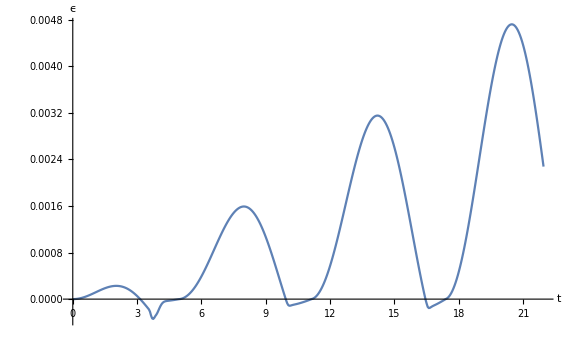

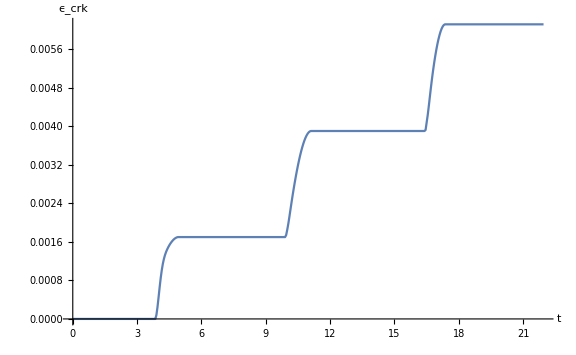

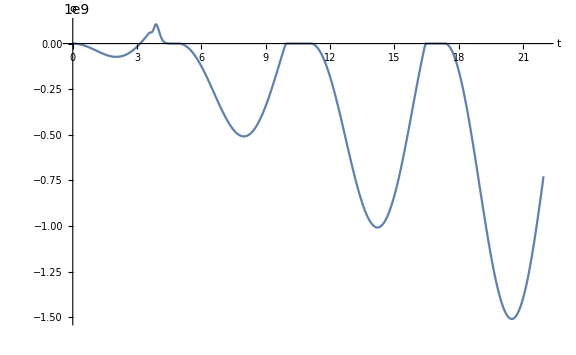

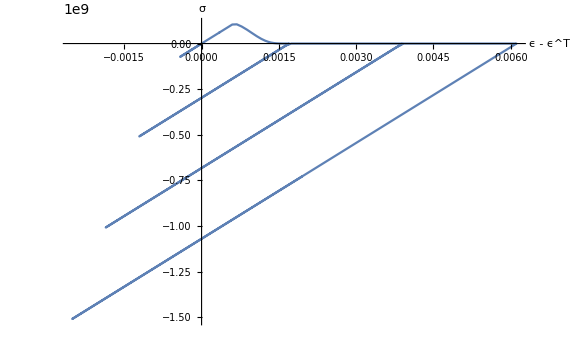

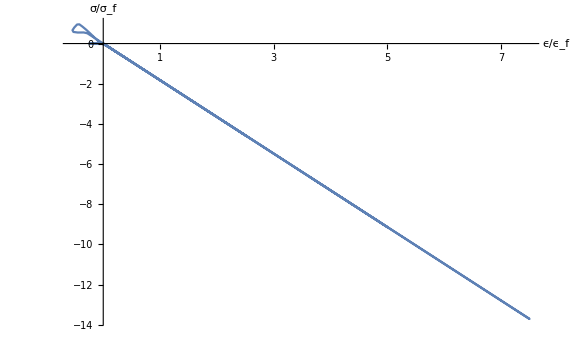

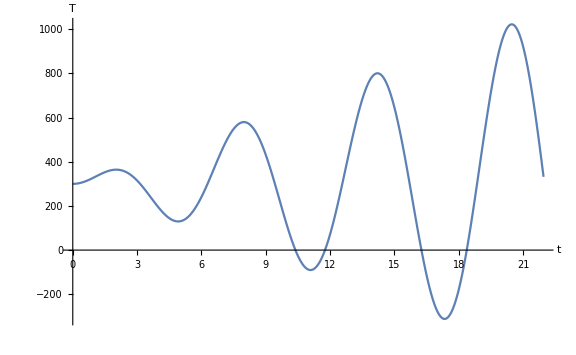

```mathematica
tϵ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, -1⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦i, 2, 5⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦i, 2, 4⟧/ϵf, data⟦i, 2, 3⟧/σf}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]
tT = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 2⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ]
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```

```mathematica
Solve[{x == 1, y == 1}, {x, y}]⟦All, 1⟧
```

{x→1}